```mathematica
(* Subscript[I, 2](l,L) at 2 T_c with free b.c.
=c/2 ln[(f(l/L) f((L-l)/L))/(√L f(1))]
where f(x)=Dedekindeta(ix) *)
```

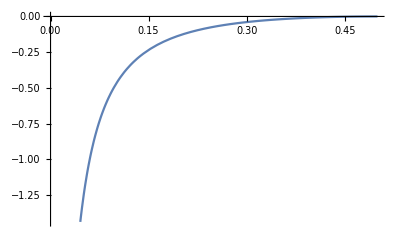

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(****************************************)
Clear[data,l];
data=Import["c.txt","Table"];
l=ListPlot3D[data,InterpolationOrder->3,ColorFunction->"SouthwestColors",AxesLabel->{"D_c","T_c","c"},PlotRange->{0.5,.9}]
ListDensityPlot[data,InterpolationOrder->6,Axes->True,FrameLabel->{"D_c","T_c"},PlotRange->{0.5,.9},PlotLegends->Automatic]
cplot=ListContourPlot[data,InterpolationOrder->3,Axes->True,DataRange->{{1.89,1.93},{0.3,0.85}},FrameLabel->{"D_c","T_c"},PlotRange->{0.55,.85},Contours->{0.55,0.65,0.75,0.85},PlotLegends->Automatic]
(*ListContourPlot[data,InterpolationOrder->6,Axes->True,FrameLabel->{"D_c","T_c"},PlotLegends->Automatic,Contours->{0.2,0.7,0.6,0.8}]*)

Export["countour_c.jpg",cplot]
```

-Graphics3D-

-Graphics-

-Graphics-

countour_c.jpg

-Graphics-

countour_c.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
(****************************************)
Clear[data,l];
data=Import["chi2.txt","Table"];
ListPlot3D[data,InterpolationOrder->3,ColorFunction->"SouthwestColors",PlotRange->{0,100},AxesLabel->{"D_c","T_c","c"}]
chiplot=ListContourPlot[data,InterpolationOrder->6,Axes->True,FrameLabel->{"D_c","T_c"},Contours->{0,10,100,100,500},PlotRange->{0,1000},PlotLegends->Automatic, ColorFunction->"Pastel"]
(*ListContourPlot[data,InterpolationOrder->6,Axes->True,FrameLabel->{"D_c","T_c"},PlotLegends->Automatic,Contours->{0.2,0.7,0.6,0.8}]*)

Export["chisq.jpg",cplot]
```

-Graphics3D-

-Graphics-

chisq.jpg